```mathematica
(*This file is used to produce detailed balance plots*)
```

### (a) The phase diagram

```mathematica
(*export the data*)
(*note: the filepath should be modified accordingly*)
Stabtest=Import["/users/linzhixing/desktop/data/stab.txt", "Table"];
```

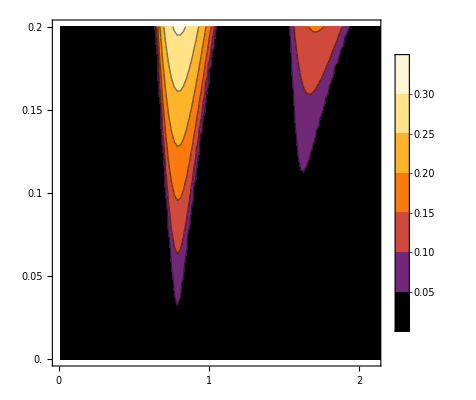

```mathematica
p1=ListContourPlot[Stabtest,PlotRange->{{0,2.1},Automatic,{0,Max[Chop[Flatten[Stabtest[[All,{3}]]]]]}},ColorFunction->Function[{z},ColorData["SunsetColors"][z-0.05]],
(*Epilog->{LightMagenta,Triangle[{{1.25,0.104},{1.21,0.0975},{1.29,0.0975}}],LightMagenta,Rectangle[{0.77,0.097},{0.83,0.103}]},*)
PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20,FontColor->Black}],
FrameTicks->{{Range[0,0.2,0.05],None},{Range[0,4,1],None}},
FrameTicksStyle->Directive[Black,22],
FrameStyle->AbsoluteThickness[1.5],
Frame->True]
```

```mathematica
boundplot=Import["/users/linzhixing/desktop/data/boundary.txt", "Table"];
```

```mathematica
ListDensityPlot[boundplot]
```

-Graphics-

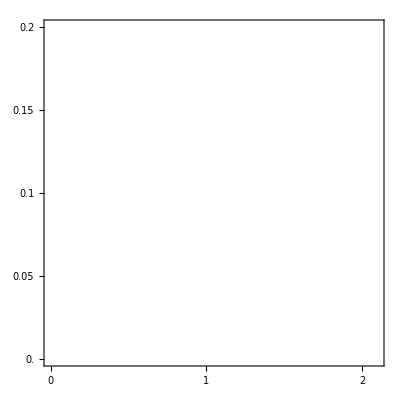

```mathematica
p2=ListContourPlot[boundplot,PlotRange->{{0,2.1},Automatic,{0,Max[Chop[Flatten[boundplot[[All,{3}]]]]]}},ColorFunction->Function[{z},ColorData["SunsetColors"][z-0.05]],
Contours->{0.0002},ContourShading->None,InterpolationOrder->10,ContourStyle->Directive[White,Thickness[0.006],Dashing[{0.02, 0.02}]],
PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20,FontColor->Black}],
FrameTicks->{{Range[0,0.2,0.05],None},{Range[0,4,1],None}},
FrameTicksStyle->Directive[Black,22],
FrameStyle->AbsoluteThickness[1.5],
Frame->True]
```

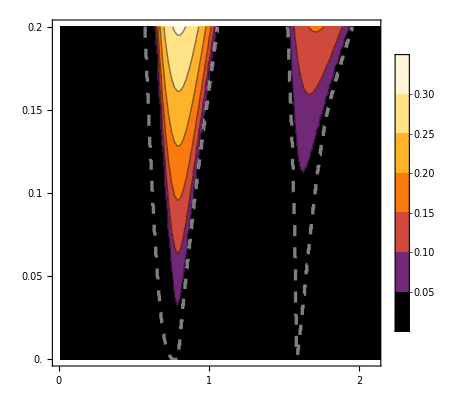

```mathematica
Show[p1,p2]
```

### (b) The ImLambda value plots

```mathematica
(*export the data*)
cv1=Import["/users/linzhixing/desktop/data/Lambda_symm_5.txt", "Table"];
cv2=Import["/users/linzhixing/desktop/data/Lambda_symm_10.txt", "Table"];
cv3=Import["/users/linzhixing/desktop/data/Lambda_symm_15.txt", "Table"];
cv4=Import["/users/linzhixing/desktop/data/Lambda_symm_18.txt", "Table"];
```

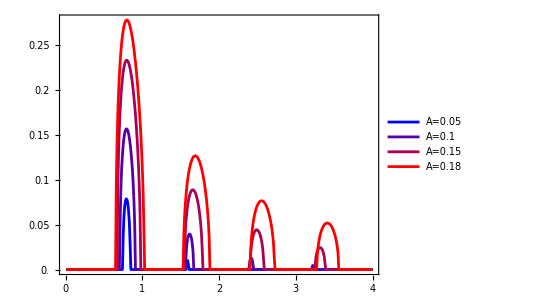

```mathematica
ListLinePlot[{Chop[cv1],Chop[cv2],Chop[cv3],Chop[cv4]},
PlotRange->Full,AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/3],Blend[{Blue,Red},2/3],Blend[{Blue,Red},1]},
PlotLegends->Placed[LineLegend[{"A=0.05", "A=0.1","A=0.15","A=0.18"},LabelStyle->{FontSize->15}],{0.75, 0.75}],
FrameTicks->{{Range[0,0.32,0.05],None},{Range[0,4,1],None}},
FrameTicksStyle->Directive[Black,18],
FrameStyle->AbsoluteThickness[1.5],
Frame->True]
```

### (c) (d) (e) The Spectrums

```mathematica
(*first define the Λ value function*)
A0=-0.3;
Λvalue[A_,ω_,q_]:=Module[{T,sol,Λ},T=(2 π)/ω;sol=NDSolve[{Rt2'[x]+1/2 q (A0+A Cos[ω x])-2 It2[x] q (1+A0+A Cos[ω x])-2 (Rt2[x]^2-It2[x]^2) q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x] q (1+A0+A Cos[ω x])-4 (Rt2[x] It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,2 T}];Λ=(1+A0)+(2I)/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rt2[x]]/.sol[[1]][[1]],{x,0,T}]-2/T NIntegrate[(A0+A Cos[ω x])Evaluate[It2[x]]/.sol[[1]][[2]],{x,0,T}];Λ];
```

```mathematica
Λvalue[0.1,1.2,1]
```

0.6-0.0724897 ⅈ

```mathematica
0.07248966655316366 2
```

0.144979

0.616602+5.44765×10^-9 ⅈ

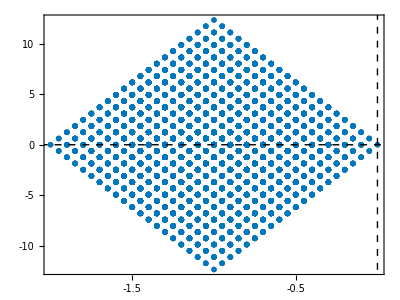

```mathematica
Λ2=Λvalue[0.1,0.8,1]
γ=0.1;
spectrum=Flatten[Table[I Λ2(m1+m2-n1-n2)-γ(m1+n1+m2+n2)/2,{m1,0,10},{n1,0,10},{m2,0,10},{n2, 0,10}]];
data=Transpose[{Re[spectrum],Im[spectrum]}];
ListPlot[DeleteCases[{Style[#,RGBColor["#0077BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#CC3311"]]&/@Select[data,#[[1]]>0&]},{}],
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,15},{0,-15}}]},{Black,Dashed,Line[{{-35,0},{2,0}}]}},
PlotStyle->{PointSize[0.010]},
FrameTicks->{{Range[-10,10,5],None},{Range[-2.5,0.5,0.5],None}},
FrameStyle->Directive[Black,25],
Frame->True]
```

0.625-0.0783474 ⅈ

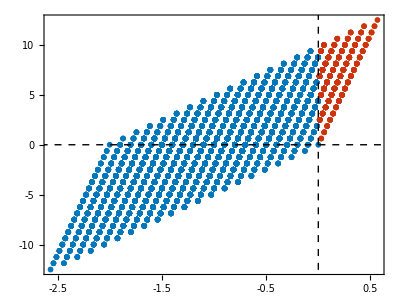

```mathematica
Λ2=Λvalue[0.1,1.25,1]
γ=0.1;
spectrum=Flatten[Table[I Λ2(m1+m2-n1-n2)-γ(m1+n1+m2+n2)/2,{m1,0,10},{n1,0,10},{m2,0,10},{n2, 0,10}]];
data=Transpose[{Re[spectrum],Im[spectrum]}];
ListPlot[DeleteCases[{Style[#,RGBColor["#0077BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#CC3311"]]&/@Select[data,#[[1]]>0&]},{}],
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,15},{0,-15}}]},{Black,Dashed,Line[{{-35,0},{2,0}}]}},
PlotStyle->{PointSize[0.010]},
FrameTicks->{{Range[-10,10,5],None},{Range[-2.5,0.5,1.0],None}},
FrameStyle->Directive[Black,25],
Frame->True]
```

0.625-0.0783474 ⅈ

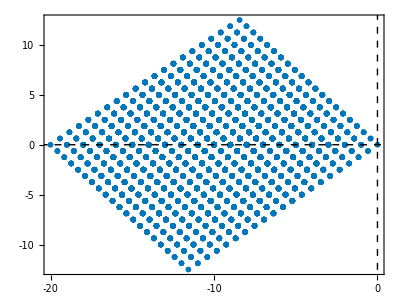

```mathematica
Λ2=Λvalue[0.1,1.25,1]
γ=1.0;
spectrum=Flatten[Table[I Λ2(m1+m2-n1-n2)-γ(m1+n1+m2+n2)/2,{m1,0,10},{n1,0,10},{m2,0,10},{n2, 0,10}]];
data=Transpose[{Re[spectrum],Im[spectrum]}];
ListPlot[DeleteCases[{Style[#,RGBColor["#0077BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#CC3311"]]&/@Select[data,#[[1]]>0&]},{}],
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,15},{0,-15}}]},{Black,Dashed,Line[{{-35,0},{2,0}}]}},
PlotStyle->{PointSize[0.010]},
FrameTicks->{{Range[-10,10,5],None},{Range[-30,2,5],None}},
FrameStyle->Directive[Black,25],
Frame->True]
```